# Algorithmic Differentiation

We need first and second derivatives for our tests and algorithms.  In the real world our constraints and cost function are defined by computer code. Algorithmic Differentiation (AD) provides ways to generate code for derivatives from the code for the functions.  It used to be called Automatic Differentiation but the folks that do it thought that gave the wrong impression and just decided to change their name but not their acronym!

First a reminder of what we know.

## Derivatives and Finite Differences

For f:ℝ→ℝ and x∈ℝ
	f'[x]=lim_(h->0) (f[x+h]-f[x])/h

For f:ℝ^n→ℝ and and x,u∈ℝ^n
	∂_u f | = | lim_(h->0) (f[x+ h u ]-f[x])/h
(∂f)/(∂x_i) | = | lim_(h->0) (f[x+ h e_i ]-f[x])/h
Df | = | {∂_1 f,∂_2 f,…,∂_n f}
where ∂_i f=∂f/∂x_i and we have skipped writing down the x dependence.

A derivative of a derivative is a second derivative.  The Hessian of  f:ℝ^n→ℝ 
is the n×n symmetric matrix of second derivatives
	(∂f)/(∂x_i∂x_j) | = | ∂_i (∂_j f) | = | ∂_j (∂_i f)
DDf_(i,j) | = | H_(i,j) | = | ∂_ij f  
Calculus courses usually cover finite Difference(FD) approximations

  | Forward Diff | Centered Diff
f'[x] | (f[x+h]-f[x])/h | (f[x+h]-f[x-h])/(2h)
f''[x] | (f[x+2h]-2f[x+h]+f[x])/h^2  | (f[x+h]-2f[x]+f[x-h])/h^2
∂_i f[x] | (f[x+he_i]-f[x])/h | (f[x+he_i]-f[x-he_i])/(2h)
∂_(i,j) f[x] | (f[x+he_i+ he_j]-f[x+he_i]- f[x+he_j]+ f[x])/h^2 | (f[x+he_i+ he_j]-f[x+he_i-he_j]- f[x+he_j-he_i]+ f[x-he_i-he_j])/h^2

Taylor Series (TS) show that centered differences are more accurate with error behavior described by the TS error terms.

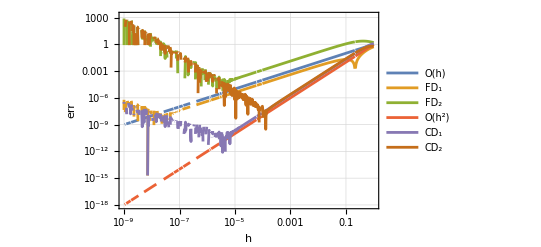

```mathematica
f[x_]:= Cos[x + Exp[ Sin[Log[1+x^2]]]]
x=1.5;
SetOptions[LogLogPlot,GridLines->Automatic,MaxRecursion->4,Frame->True];
LogLogPlot[{
h,Abs[f'[x]-(f[x+h]-f[x])/h],Abs[f''[x]-(f[x+2h]-2f[x+h]+f[x])/h^2],
h^2,Abs[f'[x]-(f[x+h]-f[x-h])/(2h)],Abs[f''[x]-(f[x+h]-2f[x]+f[x-h])/h^2]
},{h,10^-9, 1},
FrameLabel->{"h","err"},
PlotLegends->{"O(h)","FD_1","FD_2","O(h^2)","CD_1","CD_2"}]
```

## Algorithmic Differentiation

Every single piece of a computer function is either arithmetic, logic, or a call to a special function that we  know the derivative of.  Each of those pieces (except the logic) is differentiable. So we can go line by line and differentiate.  At the bottom level this is all AD is.  There are two common ways to accumulate the derivatives.  Forward or Backward in the flow of the program.  Forward is easy to understand and code. Backwards is theoretically more efficient for computing the gradient of a function f:ℝ^n→ℝ.

### Basic Example: Forward Mode

This is much clearer with an example. The function from f:ℝ^3→ℝ^2
	f[x]={x_3+x_1 x_2,x_1 x_2+Cos[x_1+Sin[x_3]]}
is easy to implement.  Here is code to compute it in small steps with the work variables stored in a sequence of “work” variables.

```mathematica
f[{x1_,x2_,x3_}]:= Module[{w1,w2,w3,w4,w5},
w1=x1*x2;
w2=x3+x1*x2;
w3=Sin[x3];
w4=x1+w3;
w5=Cos[w4];
{w2,w5}
]
```

Functions always need to be tested.  This is far from a complete test!

```mathematica
x={0.2,1.4,0.6};
f[x]
```

Here is a forward mode Algorithmic Differentiation (AD) code for the function.

```mathematica
df[{x1_,x2_,x3_},{dx1_,dx2_,dx3_}]:= Module[
{w1,w2,w3,w4,w5,dw1,dw2,dw3,dw4,dw5},
dw1=dx1*x2+x1*dx2;
w1=x1*x2;
dw2=dx3+dw1;
w2=x3+w1;
dw3=Cos[x3]*dx3;
w3=Sin[x3];
dw4=dx1+dw3;
w4=x1+w3;
dw5=-Sin[w4]*dw4;
w5=Cos[w4];
{{w2,w5},{dw2,dw5}}
]
```

We need to test this trick.

```mathematica
x={0.2,1.4,0.6};
dx={0.2,1.6,-3.4};
h=0.01;
{{f1,f2},{df1,df2}}=df[x,dx]
Plot[{f[x+ h dx]⟦1⟧,f[x+ h dx]⟦2⟧,
f1+h df1,f2+h df2},
{h, -0.5,0.5},
PlotLegends->{"1","2"}]
```

You can do the same thing again to get directional second derivatives as well.

### Basic Example: Backward Mode

Backwards mode computes and stores the multipliers for the derivatives.  It then works backwards from seeds of the output to compute derivatives. One way to think about this is as backsubstitution in a triangular matrix of sensitivities.

This is much clearer with an example. The function from f:ℝ^3→ℝ^2
	f[x]={x_3+x_1 x_2,x_1 x_2+Cos[x_1+Sin[x_3]]}
is easy to implement.  Here is code to compute it in small steps. The work variables are stored in a sequence of “work” variables.  We are going to modify the forward mode code to store the sensitivities of the work variables are in a sparse array.

```mathematica
Df[{x1_,x2_,x3_},{df1_,df2_}]:= Module[
{w1,w2,w3,w4,w5,dw1,dw2,dw3,dw4,dw5},
dw1=dx1*x2+x1*dx2;
w1=x1*x2;
dw2=dx3+dw1;
w2=x3+w1;
dw3=Cos[x3]*dx3;
w3=Sin[x3];
dw4=dx1+dw3;
w4=x1+w3;
dw5=-Sin[w4]*dw4;
w5=Cos[w4];
(* Back Substitution *)
(* Solving for {dx1,dx2,dx3} for a given {df1,df2} *)
 {w2,w5}
]
```

### Implementations and Resources

There are several ways to implement AD.

Tapenade http://www-tapenade.inria.fr:8080/tapenade/index.jsp takes C or Fortran code and automatically returns code (forward or reverse mode) for derivatives.  Not surprisingly this is called “code rewrite”.  There are similar tools in Julia.

You can implement Forward Mode by overloading operators to compute with Dual Numbers e.g.
	(x+ϵ dx)(y+ϵ dy)=x y + ϵ (dx y + y dx)
and 
	cos(x+ϵ dx)=cos(x)-ϵ sin(x) dx
Some thought is needed to do second (or higher) derivatives this way to label the variations in some way.  Look at https://www.google.com/search?q=perturbation+confusion
for some useful discussion. Julia implements forward mode AD using Dual Numbers in the ForwardDiff package. Add “Julia” to the Google query to find out that the Julia developers fell into confusion and then fixed it! It does seem mandatory to ignore this difficulty at first.